```mathematica
mat=Import["input25.txt","Table"];
```

```mathematica
names={};
```

```mathematica
Do[AppendTo[names,mat[[i]][[j]]],{i,1,Length[mat]},{j,1,Length[mat[[i]]]}]
```

```mathematica
names=DeleteDuplicates[names];
mp=Association[Table[names[[i]]->i,{i,1,Length[names]}]];
```

```mathematica
adj={};
Do[AppendTo[adj,mp[[mat[[i]][[j]]]]<->mp[[mat[[i]][[1]]]] ],{i,1,Length[mat]},{j,1,Length[mat[[i]]]}]
```

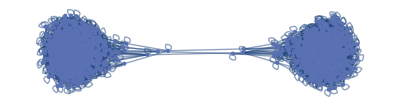

```mathematica
g = AdjacencyGraph[AdjacencyMatrix[adj]]
cut=FindMinimumCut[g];
```

```mathematica
Length[cut[[2]][[1]]]*Length[cut[[2]][[2]]]
```

514794